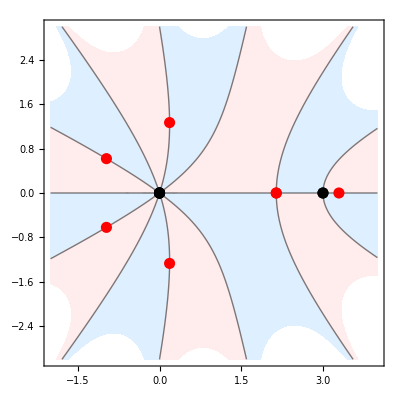

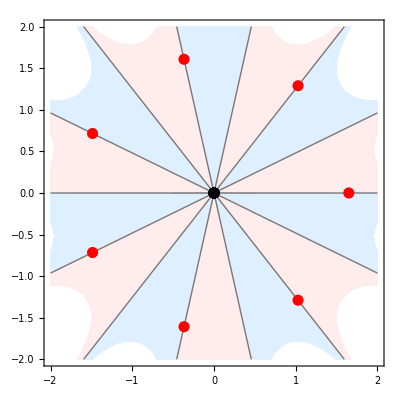

```mathematica
cz=15/7;
cw=cz^5*(cz-3)^2;
diag=1+I;
size=PointSize[0.02];
proc[f_,a_,b_]:=Module[{cp,lp1,lp2,z1,z2},
z1=z/.Solve[f==0];
z2=z/.Solve[f==cw];
cp=ComplexContourPlot[Im[f],{z,a-b*diag,a+b*diag},
Contours->{0},ContourShading->{LightBlue,LightPink},PlotPoints->100];
lp1=ComplexListPlot[z1,PlotStyle->{Black,size}];
lp2=ComplexListPlot[z2,PlotStyle->{Red,size}];
Show[cp,lp1,lp2]];
p=z^5(z-3)^2;
r=Range[-Pi,Pi,Pi/7];
pz=proc[p,1,3]
pw=proc[z^7,0,2]
```